```mathematica
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

FullInflate::shdw: Symbol "FullInflate" appears in multiple contexts {"PenroseTilingFunctions`", "Global`"}; definitions in context "PenroseTilingFunctions`" may shadow or be shadowed by other definitions.

starseed::shdw: Symbol "starseed" appears in multiple contexts {"PenroseTilingFunctions`", "Global`"}; definitions in context "PenroseTilingFunctions`" may shadow or be shadowed by other definitions.

```mathematica
Inflate[starseed,1]
```

{{{0.809017+0.587785 ⅈ,0,0.618034},fat},{{0.618034,1,0.809017+0.587785 ⅈ},skinny},{{1.30902+0.951057 ⅈ,1,0.809017+0.587785 ⅈ},fat},{{0.809017+0.587785 ⅈ,0,0.190983+0.587785 ⅈ},fat},{{0.190983+0.587785 ⅈ,0.309017+0.951057 ⅈ,0.809017+0.587785 ⅈ},skinny},{{1.30902+0.951057 ⅈ,0.309017+0.951057 ⅈ,0.809017+0.587785 ⅈ},fat},{{-0.309017+0.951057 ⅈ,0,0.190983+0.587785 ⅈ},fat},{{0.190983+0.587785 ⅈ,0.309017+0.951057 ⅈ,-0.309017+0.951057 ⅈ},skinny},{{-0.5+1.53884 ⅈ,0.309017+0.951057 ⅈ,-0.309017+0.951057 ⅈ},fat},{{-0.309017+0.951057 ⅈ,0,-0.5+0.363271 ⅈ},fat},{{-0.5+0.363271 ⅈ,-0.809017+0.587785 ⅈ,-0.309017+0.951057 ⅈ},skinny},{{-0.5+1.53884 ⅈ,-0.809017+0.587785 ⅈ,-0.309017+0.951057 ⅈ},fat},{{-1.,0,-0.5+0.363271 ⅈ},fat},{{-0.5+0.363271 ⅈ,-0.809017+0.587785 ⅈ,-1.},skinny},{{-1.61803,-0.809017+0.587785 ⅈ,-1.},fat}}

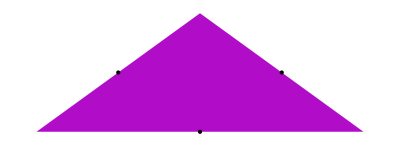

```mathematica
Show[See@{unitfat},Graphics[Point/@Coor@Midpoints[unitfat]]]
```

```mathematica
??IfFat
```

T if the triangle is fat, F if skinny

IfFat[t_,T_,F_]:=If[Last[t]==fat,T,F]

Rhomb[{{a_,b_,c_},f_}]:={{a,a-c+b,b,c},f}

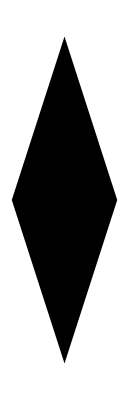

```mathematica
Graphics[(Polygon/@Coor/@PathTriangles@Rhomb@unitskinny)]
```

```mathematica
TestPoints:=Graphics@{Yellow,EdgeForm[Black],{Triangle@Coor@ #,{PointSize[Large],Transpose[{{Red,Green,Blue},Point/@Coor@#}]}}}&
```

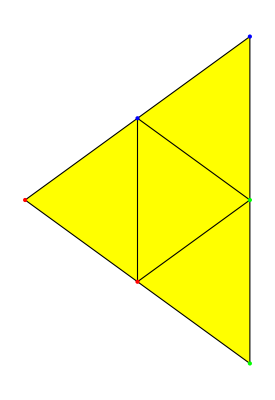
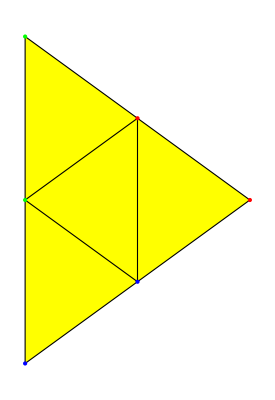

```mathematica
Show/@Transpose[{TestPoints/@(PathTriangles@Rhomb@unitfat),TestPoints/@(Midpoints/@PathTriangles@Rhomb@unitfat)}]
```

```mathematica
Midpoints/@PathTriangles@Rhomb@unitskinny
```

{{0.,0.25+0.769421 ⅈ,-0.25+0.769421 ⅈ},{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.}}

```mathematica
SeeTri[points_]:=Graphics@Polygon@Coor@points

Midpoints[{A_,B_,C_}]:=1/2{B+A,B+C,A+C}

Orientation[{A_,B_,C_}]:=Sign@Det[{Flatten@Coor@{B-A},Flatten@Coor@{((C-B))}}]

OrientTriangle[{A_,B_,C_}]:=If[Orientation[{A,B,C}]==1,{A,B,C},{A,C,B}]

PathTriangles[{{A_,P_,B_,C_},t_}]:=If[t=="fat",{{A,P,C},{B,C,P}},{{A,B,C},{A,P,B}}]

MakePathTriangles[list_]:=OrientTriangle/@Flatten[PathTriangles/@list,1]

EqualQ[list_,element_]:=Equal[#,element]&/@list

SharedSide[list_,element_]:=Select[list,MemberQ[n_/;Abs[n-element]<10^-10]]

FindNextTriangle[list_,prev_,midpoint_]:=DeleteCases[SharedSide[list,midpoint],prev]

ChangeTriangle[list_,prev_,midpoint_]:=Flatten@FindNextTriangle[list,prev,midpoint]

Go[{starttriangle_,startside_},dir_]:=Part[starttriangle,Mod[startside+dir,3,1]]

PathStep[list_,{starttriangle_,startmidpoint_,dir_}]:=
Module[{nexttriangle,nextmidpoint,startside=First@Flatten@Position[starttriangle,n_/;Abs[n-startmidpoint]<10^-10],nextdir=-1*dir},nextmidpoint=Go[{starttriangle,startside},dir];
{ChangeTriangle[list,starttriangle,nextmidpoint],nextmidpoint,nextdir}]

MakePath[list_,{starttriangle_,startmidpoint_,dir_}]:=DeleteCases[NestWhileList[PathStep[list,#]&,{starttriangle,startmidpoint,dir},UnsameQ,All],{{},{}[[_]],_}]

PathPoints[list_]:=Line/@Partition[Coor@list[[All,2]],2,1]
```

```mathematica
Mod[4,3,1]
```

1

```mathematica
StopCondition=UnsameQ&&FreeQ[{}]
```

UnsameQ&&FreeQ[{}]

```mathematica
StopTest[{1,2,3}]
```

True

```mathematica
Midpoints/@PathTriangles@Rhomb@unitskinny
FindNextTriangle[%,%[[1]],0.]
```

```mathematica
Unsame
```

```mathematica
ChangeTriangle[Midpoints/@PathTriangles@Rhomb@unitskinny,{0.,0.25+0.7694208842938134 ⅈ,-0.25+0.7694208842938134 ⅈ},0.]
```

{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.}

```mathematica
GoRight[{{-0.25-0.7694208842938134 ⅈ,0.25-0.7694208842938134 ⅈ,0.},3}]
```

-0.25-0.769421 ⅈ

```mathematica
testtris=Midpoints/@PathTriangles@Rhomb@unitskinny
```

{{0.,0.25+0.769421 ⅈ,-0.25+0.769421 ⅈ},{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.}}

```mathematica
First@Flatten@Position[{0.,0.25+0.7694208842938134 ⅈ,-0.25+0.7694208842938134 ⅈ},0.25+0.7694208842938134 ⅈ]
```

```mathematica
nxt=Go[{{0.,0.25+0.7694208842938134 ⅈ,-0.25+0.7694208842938134 ⅈ},2},-1]
```

```mathematica
ChangeTriangle[testtris,testtris[[1]],nxt]
```

{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.}

```mathematica
PathStep[testtris,{testtris[[1]],testtris[[1,2]]},-1]
```

{{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.},0.,1}

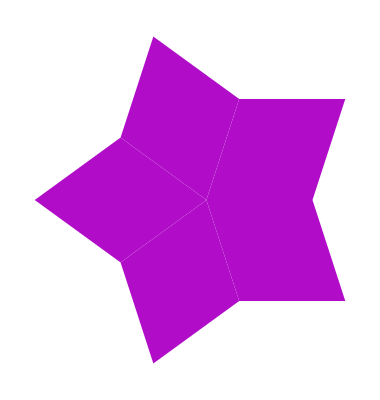

```mathematica
See@(FullInflate[starseed,0])
```

```mathematica
testtris=Midpoints/@MakePathTriangles@FullInflate[starseed,6];
```

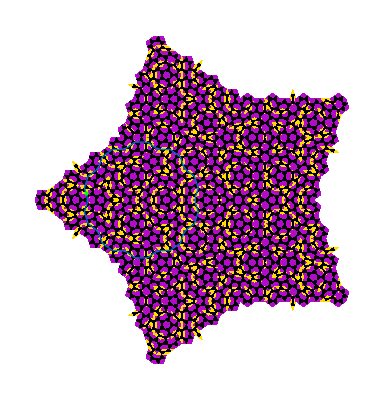

```mathematica
Show[See@(FullInflate[starseed,5]),SeeTri/@testtris,Graphics[{NiceBlue,Thick,#}]&/@PathPoints@MakePath[testtris,{testtris[[56]],testtris[[56,3]],1}],Graphics[{Thick,Green,Point[Coor@{testtris[[56,3]]}]}]]
```

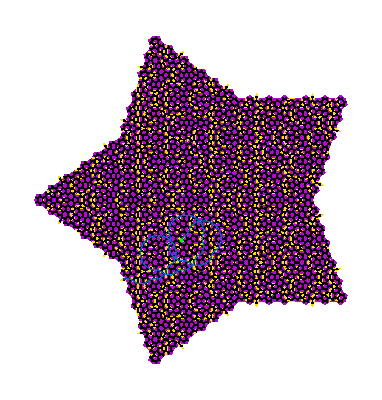

```mathematica
Show[See@(FullInflate[starseed,6]),SeeTri/@testtris,Graphics[{NiceBlue,Thick,#}]&/@PathPoints@MakePath[testtris,{testtris[[1587]],testtris[[1587,3]],-1}],Graphics[{Thick,Green,Point[Coor@{testtris[[1587,3]]}]}]]
```

```mathematica
MakePath[testtris,{testtris[[56]],testtris[[56,3]],1}];
```

```mathematica
PathPoints@MakePath[testtris,{testtris[[3]],testtris[[3,3]],-1}]
```

```mathematica
MakePath[testtris,{testtris[[87]],testtris[[87,3]],1}]
```

{{{-1.01393-0.40615 ⅈ,-1.05902-0.40615 ⅈ,-1.04508-0.449028 ⅈ},-1.04508-0.449028 ⅈ,1},{{-1.01393-0.40615 ⅈ,-0.986068-0.40615 ⅈ,-1.-0.363271 ⅈ},-1.01393-0.40615 ⅈ,-1},{{-1.-0.363271 ⅈ,-0.986068-0.320393 ⅈ,-1.01393-0.320393 ⅈ},-1.-0.363271 ⅈ,1},{{-0.935661-0.336771 ⅈ,-0.949593-0.293893 ⅈ,-0.986068-0.320393 ⅈ},-0.986068-0.320393 ⅈ,-1},{{-0.963525-0.251014 ⅈ,-0.949593-0.293893 ⅈ,-0.913119-0.267392 ⅈ},-0.949593-0.293893 ⅈ,1},{{-0.913119-0.267392 ⅈ,-0.868034-0.267392 ⅈ,-0.881966-0.224514 ⅈ},-0.913119-0.267392 ⅈ,-1},{{-0.881966-0.224514 ⅈ,-0.868034-0.181636 ⅈ,-0.913119-0.181636 ⅈ},-0.881966-0.224514 ⅈ,1},{{-0.854102-0.138757 ⅈ,-0.868034-0.181636 ⅈ,-0.822949-0.181636 ⅈ},-0.868034-0.181636 ⅈ,-1},{{-0.822949-0.0958789 ⅈ,-0.868034-0.0958789 ⅈ,-0.854102-0.138757 ⅈ},-0.854102-0.138757 ⅈ,1},{{-0.772542-0.112257 ⅈ,-0.786475-0.0693786 ⅈ,-0.822949-0.0958789 ⅈ},-0.822949-0.0958789 ⅈ,-1},{{-0.800407-0.0265003 ⅈ,-0.786475-0.0693786 ⅈ,-0.75-0.0428784 ⅈ},-0.786475-0.0693786 ⅈ,1},{{-0.75-0.0428784 ⅈ,-0.704915-0.0428784 ⅈ,-0.718847+2.08167×10^-17 ⅈ},-0.75-0.0428784 ⅈ,-1},{{-0.718847-2.08167×10^-17 ⅈ,-0.704915+0.0428784 ⅈ,-0.75+0.0428784 ⅈ},-0.718847+2.08167×10^-17 ⅈ,1},{{-0.690983+0.0857567 ⅈ,-0.704915+0.0428784 ⅈ,-0.65983+0.0428784 ⅈ},-0.704915+0.0428784 ⅈ,-1},{{-0.699593+0.112257 ⅈ,-0.690983+0.0857567 ⅈ,-0.654508+0.112257 ⅈ},-0.690983+0.0857567 ⅈ,1},{{-0.654508+0.112257 ⅈ,-0.609424+0.112257 ⅈ,-0.618034+0.138757 ⅈ},-0.654508+0.112257 ⅈ,-1},{{-0.586881+0.181636 ⅈ,-0.631966+0.181636 ⅈ,-0.618034+0.138757 ⅈ},-0.618034+0.138757 ⅈ,1},{{-0.586881+0.181636 ⅈ,-0.559017+0.181636 ⅈ,-0.572949+0.224514 ⅈ},-0.586881+0.181636 ⅈ,-1},{{-0.572949+0.224514 ⅈ,-0.559017+0.267392 ⅈ,-0.586881+0.267392 ⅈ},-0.572949+0.224514 ⅈ,1},{{-0.50861+0.251014 ⅈ,-0.522542+0.293893 ⅈ,-0.559017+0.267392 ⅈ},-0.559017+0.267392 ⅈ,-1},{{-0.536475+0.336771 ⅈ,-0.522542+0.293893 ⅈ,-0.486068+0.320393 ⅈ},-0.522542+0.293893 ⅈ,1},{{-0.486068+0.320393 ⅈ,-0.440983+0.320393 ⅈ,-0.454915+0.363271 ⅈ},-0.486068+0.320393 ⅈ,-1},{{-0.454915+0.363271 ⅈ,-0.440983+0.40615 ⅈ,-0.486068+0.40615 ⅈ},-0.454915+0.363271 ⅈ,1},{{-0.427051+0.449028 ⅈ,-0.440983+0.40615 ⅈ,-0.395898+0.40615 ⅈ},-0.440983+0.40615 ⅈ,-1},{{-0.435661+0.475528 ⅈ,-0.427051+0.449028 ⅈ,-0.390576+0.475528 ⅈ},-0.427051+0.449028 ⅈ,1},{{-0.390576+0.475528 ⅈ,-0.345492+0.475528 ⅈ,-0.354102+0.502029 ⅈ},-0.390576+0.475528 ⅈ,-1},{{-0.322949+0.544907 ⅈ,-0.368034+0.544907 ⅈ,-0.354102+0.502029 ⅈ},-0.354102+0.502029 ⅈ,1},{{-0.322949+0.544907 ⅈ,-0.295085+0.544907 ⅈ,-0.309017+0.587785 ⅈ},-0.322949+0.544907 ⅈ,-1},{{-0.309017+0.587785 ⅈ,-0.295085+0.630664 ⅈ,-0.322949+0.630664 ⅈ},-0.309017+0.587785 ⅈ,1},{{-0.244678+0.614286 ⅈ,-0.25861+0.657164 ⅈ,-0.295085+0.630664 ⅈ},-0.295085+0.630664 ⅈ,-1},{{-0.272542+0.700042 ⅈ,-0.25861+0.657164 ⅈ,-0.222136+0.683664 ⅈ},-0.25861+0.657164 ⅈ,1},{{-0.222136+0.683664 ⅈ,-0.177051+0.683664 ⅈ,-0.190983+0.726543 ⅈ},-0.222136+0.683664 ⅈ,-1},{{-0.190983+0.726543 ⅈ,-0.177051+0.769421 ⅈ,-0.222136+0.769421 ⅈ},-0.190983+0.726543 ⅈ,1},{{-0.163119+0.812299 ⅈ,-0.177051+0.769421 ⅈ,-0.131966+0.769421 ⅈ},-0.177051+0.769421 ⅈ,-1},{{-0.131966+0.855178 ⅈ,-0.177051+0.855178 ⅈ,-0.163119+0.812299 ⅈ},-0.163119+0.812299 ⅈ,1},{{-0.0815595+0.8388 ⅈ,-0.0954915+0.881678 ⅈ,-0.131966+0.855178 ⅈ},-0.131966+0.855178 ⅈ,-1},{{-0.109424+0.924556 ⅈ,-0.0954915+0.881678 ⅈ,-0.059017+0.908178 ⅈ},-0.0954915+0.881678 ⅈ,1},{{-0.059017+0.908178 ⅈ,-0.013932+0.908178 ⅈ,-0.027864+0.951057 ⅈ},-0.059017+0.908178 ⅈ,-1},{{-0.027864+0.951057 ⅈ,-0.013932+0.993935 ⅈ,-0.059017+0.993935 ⅈ},-0.027864+0.951057 ⅈ,1},{{-2.08167×10^-17+1.03681 ⅈ,-0.013932+0.993935 ⅈ,0.0311529+0.993935 ⅈ},-0.013932+0.993935 ⅈ,-1},{{-0.00861046+1.06331 ⅈ,-2.08167×10^-17+1.03681 ⅈ,0.0364745+1.06331 ⅈ},-2.08167×10^-17+1.03681 ⅈ,1},{{0.0364745+1.06331 ⅈ,0.0815595+1.06331 ⅈ,0.072949+1.08981 ⅈ},0.0364745+1.06331 ⅈ,-1},{{0.104102+1.13269 ⅈ,0.059017+1.13269 ⅈ,0.072949+1.08981 ⅈ},0.072949+1.08981 ⅈ,1},{{},0.104102+1.13269 ⅈ,-1}}

```mathematica
SharedSide[list_,element_]:=Select[list,MemberQ[n_/;Abs[n-element]<10^-10]]
```

```mathematica
SharedSide[testtris,-0.7188470506254732+2.0816681711721685*^-17 ⅈ]
```

{{-0.75-0.0428784 ⅈ,-0.704915-0.0428784 ⅈ,-0.718847+2.08167×10^-17 ⅈ},{-0.718847-2.08167×10^-17 ⅈ,-0.704915+0.0428784 ⅈ,-0.75+0.0428784 ⅈ}}

```mathematica
Abs[-0.7188470506254732+2.0816681711721685*^-17 ⅈ-(-0.7188470506254732-2.0816681711721685*^-17 ⅈ)]<10^-10
```

True

```mathematica
Abs[0.+4.163336342344337*^-17 ⅈ]
```

4.16334×10^-17

```mathematica
SharedSide[SetPrecision[testtris,7],SetPrecision[-0.7188470506254732+2.0816681711721685*^-17 ⅈ,7]]
```

{{-0.75-0.042878 ⅈ,-0.704915-0.042878 ⅈ,-0.7188471+0. ⅈ},{-0.7188471+0. ⅈ,-0.704915+0.042878 ⅈ,-0.75+0.042878 ⅈ}}

```mathematica
-0.71884705062547316067878000467317178845`7.+0``16.68158849812727 ⅈ == -0.7188470506254732+2.0816681711721685*^-17 ⅈ
```

False

```mathematica
Select[SetPrecision[testtris,5],MemberQ[SetPrecision[-0.7188470506254732+2.0816681711721685*^-17 ⅈ,5]]]
```

{{-0.75-0.0429 ⅈ,-0.70492-0.0429 ⅈ,-0.71885+0. ⅈ},{-0.71885+0. ⅈ,-0.70492+0.0429 ⅈ,-0.75+0.0429 ⅈ}}

```mathematica
RoundComplex[num_,n_]:=Complex[N[Re[num],n],N[Im[num],n]]
```

```mathematica
RoundComplex[-0.05901699437494744+0.7694208842938133 ⅈ,2]
```

-0.059017+0.769421 ⅈ

```mathematica
N[-0.05901699437494744+0.7694208842938133 ⅈ,1]===N[-0.05901699437494748+0.7694208842938133 ⅈ,1]
```

False

```mathematica
N[-0.05901699437494744,2]
```

-0.059017

```mathematica
-0.05901699437494744+0.7694208842938133 ⅈ
-0.05901699437494748+0.7694208842938133 ⅈ
```

-0.059017+0.769421 ⅈ

-0.059017+0.769421 ⅈ

```mathematica
FullForm[-0.05901699437494744+0.7694208842938133 ⅈ]
FullForm[-0.05901699437494748+0.7694208842938133 ⅈ]
```

Complex[-0.059017,0.769421]

Complex[-0.059017,0.769421]

```mathematica
Position[{a,b,c,2,2.},2]
```

{{4}}

```mathematica
SharedSide[testtris,-0.05901699437494748+0.7694208842938133 ⅈ]
```

{{-0.404508+0.657164 ⅈ,-0.154508+0.475528 ⅈ,-0.059017+0.769421 ⅈ},{0.25+0.769421 ⅈ,0.+0.951057 ⅈ,-0.059017+0.769421 ⅈ}}

```mathematica
ChangeTriangle[testtris,{0.25+0.7694208842938133 ⅈ,0.+0.9510565162951535 ⅈ,-0.05901699437494744+0.7694208842938133 ⅈ},-0.05901699437494748+0.7694208842938133 ⅈ]
```

```mathematica
Flatten@Position[{-0.4045084971874737+0.657163890148917 ⅈ,-0.15450849718747373+0.47552825814757677 ⅈ,-0.05901699437494748+0.7694208842938133 ⅈ},-0.05901699437494748+0.7694208842938133 ⅈ]
```

{3}

```mathematica
MemberQ[testtris[[25]],]
```

True

```mathematica
MemberQ[testtris[[25]],_==testtris[[25,3]]]
```

False

```mathematica
{-0.05901699437494748+0.769420884293813 ⅈ==testtris[[25,3]]}
```

{True}

False

{{{-0.904508+0.293893 ⅈ,-1.21353+0.293893 ⅈ,-1.11803+0.587785 ⅈ},-0.904508+0.293893 ⅈ,1},{{-1.52254+0.293893 ⅈ,-1.21353+0.293893 ⅈ,-1.30902},-1.21353+0.293893 ⅈ,-1},{{},-1.52254+0.293893 ⅈ,1}}

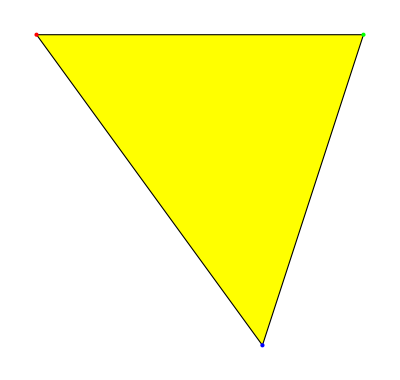
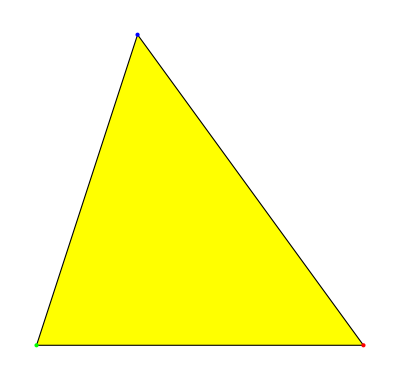
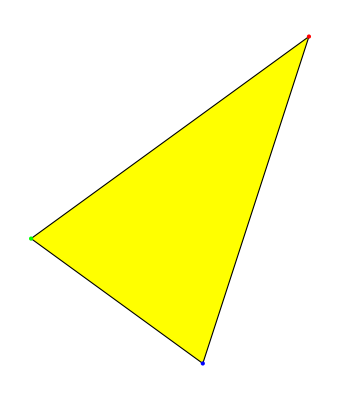
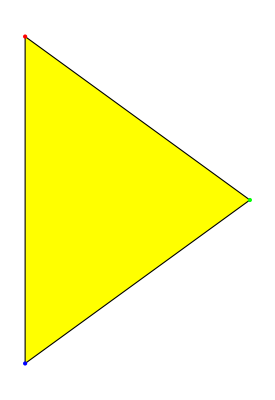
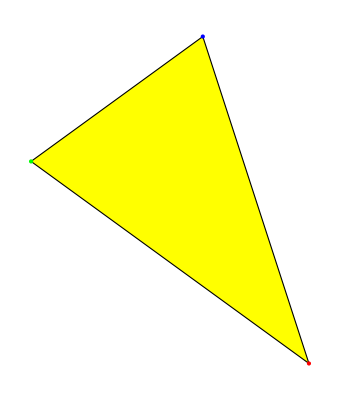
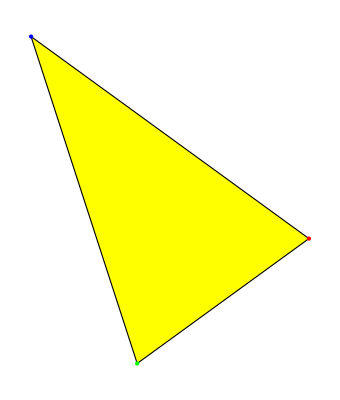
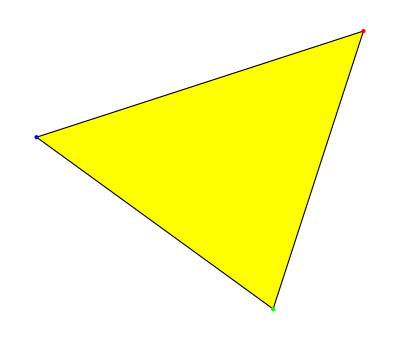
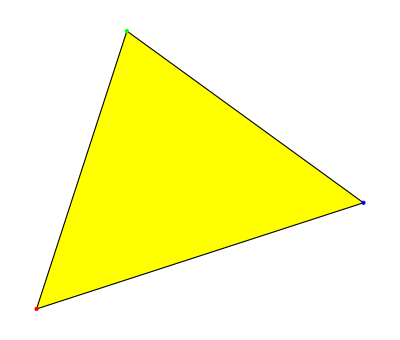

```mathematica
MakePath[testtris,{testtris[[4]],testtris[[4,1]],1}]
```

```mathematica
MakePath[testtris,{testtris[[7]],testtris[[7,1]],1}];
TestPoints/@Most@%[[All,1]]
Orientation/@Most@%%[[All,1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-1,-1,-1,-1,-1,1,-1,-1}

```mathematica
Coor[{0.30901699437494745+0. ⅈ}]
```

{{0.309017,0.}}

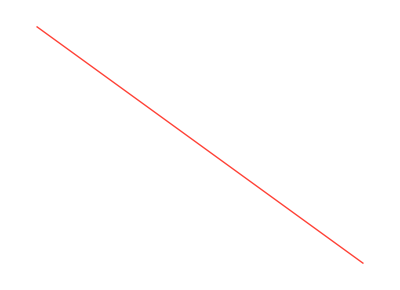
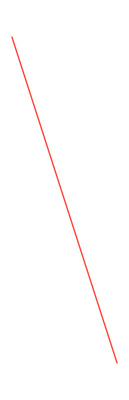
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[{NiceRed,Thick,#}]&/@PathPoints@MakePath[testtris,{testtris[[3]],testtris[[3,1]],-1}]
```

```mathematica
Line
```

```mathematica
TestPointsRhombs:=Graphics@{Yellow,EdgeForm[Black],{Polygon@Coor@ #,{PointSize[Large],Transpose[{{Red,Green,Blue,Purple},Point/@Coor@#}]}}}&
```

```mathematica
FullInflate[{unitfat},0]
```

{{{-0.809017,-1.11022×10^-16+0.587785 ⅈ,0.809017,1.11022×10^-16-0.587785 ⅈ},fat}}

```mathematica
TestPointsRhombs:=Graphics@{Yellow,EdgeForm[Black],{Polygon@Coor@ #,{PointSize[Large],Transpose[{{Red,Green,Blue,Purple},Point/@Coor@#}]}}}&
```

```mathematica
testtris=Midpoints/@MakePathTriangles@FullInflate[starseed,1]
```

{{-1.52254-0.293893 ⅈ,-1.21353-0.293893 ⅈ,-1.30902},{-0.904508-0.293893 ⅈ,-1.21353-0.293893 ⅈ,-1.11803-0.587785 ⅈ},{-1.30902,-1.21353+0.293893 ⅈ,-1.52254+0.293893 ⅈ},{-1.11803+0.587785 ⅈ,-1.21353+0.293893 ⅈ,-0.904508+0.293893 ⅈ},{-0.75-0.181636 ⅈ,-0.5+0. ⅈ,-0.75+0.181636 ⅈ},{-0.25+0.181636 ⅈ,-0.5+0. ⅈ,-0.25-0.181636 ⅈ},{-0.404508-1.24495 ⅈ,-0.654508-1.06331 ⅈ,-0.75-1.35721 ⅈ},{-0.904508-0.881678 ⅈ,-0.654508-1.06331 ⅈ,-0.559017-0.769421 ⅈ},{-0.190983-1.53884 ⅈ,-0.0954915-1.24495 ⅈ,-0.404508-1.24495 ⅈ},{0.-0.951057 ⅈ,-0.0954915-1.24495 ⅈ,0.213525-1.24495 ⅈ},{-0.75+1.35721 ⅈ,-0.654508+1.06331 ⅈ,-0.404508+1.24495 ⅈ},{-0.559017+0.769421 ⅈ,-0.654508+1.06331 ⅈ,-0.904508+0.881678 ⅈ},{-0.404508+1.24495 ⅈ,-0.0954915+1.24495 ⅈ,-0.190983+1.53884 ⅈ},{0.213525+1.24495 ⅈ,-0.0954915+1.24495 ⅈ,0.+0.951057 ⅈ},{-0.75-0.181636 ⅈ,-0.904508-0.293893 ⅈ,-0.654508-0.475528 ⅈ},{-0.654508-0.475528 ⅈ,-0.559017-0.769421 ⅈ,-0.404508-0.657164 ⅈ},{-0.654508+0.475528 ⅈ,-0.904508+0.293893 ⅈ,-0.75+0.181636 ⅈ},{-0.404508+0.657164 ⅈ,-0.559017+0.769421 ⅈ,-0.654508+0.475528 ⅈ},{-0.059017-0.769421 ⅈ,-0.154508-0.475528 ⅈ,-0.404508-0.657164 ⅈ},{-0.25-0.181636 ⅈ,-0.154508-0.475528 ⅈ,0.0954915-0.293893 ⅈ},{-0.404508+0.657164 ⅈ,-0.154508+0.475528 ⅈ,-0.059017+0.769421 ⅈ},{0.0954915+0.293893 ⅈ,-0.154508+0.475528 ⅈ,-0.25+0.181636 ⅈ},{-0.059017-0.769421 ⅈ,0.-0.951057 ⅈ,0.25-0.769421 ⅈ},{0.25-0.769421 ⅈ,0.559017-0.769421 ⅈ,0.5-0.587785 ⅈ},{0.25+0.769421 ⅈ,0.+0.951057 ⅈ,-0.059017+0.769421 ⅈ},{0.5+0.587785 ⅈ,0.559017+0.769421 ⅈ,0.25+0.769421 ⅈ},{0.713525-0.293893 ⅈ,0.904508-0.293893 ⅈ,0.809017},{0.809017,0.904508+0.293893 ⅈ,0.713525+0.293893 ⅈ},{0.713525-0.293893 ⅈ,0.404508-0.293893 ⅈ,0.5-0.587785 ⅈ},{0.0954915-0.293893 ⅈ,0.404508-0.293893 ⅈ,0.309017-1.11022×10^-16 ⅈ},{0.5+0.587785 ⅈ,0.404508+0.293893 ⅈ,0.713525+0.293893 ⅈ},{0.309017+1.11022×10^-16 ⅈ,0.404508+0.293893 ⅈ,0.0954915+0.293893 ⅈ},{1.05902-0.769421 ⅈ,0.809017-0.951057 ⅈ,1.05902-1.13269 ⅈ},{0.559017-1.13269 ⅈ,0.809017-0.951057 ⅈ,0.559017-0.769421 ⅈ},{1.40451-0.657164 ⅈ,1.15451-0.475528 ⅈ,1.05902-0.769421 ⅈ},{0.904508-0.293893 ⅈ,1.15451-0.475528 ⅈ,1.25-0.181636 ⅈ},{1.05902+1.13269 ⅈ,0.809017+0.951057 ⅈ,1.05902+0.769421 ⅈ},{0.559017+0.769421 ⅈ,0.809017+0.951057 ⅈ,0.559017+1.13269 ⅈ},{1.05902+0.769421 ⅈ,1.15451+0.475528 ⅈ,1.40451+0.657164 ⅈ},{1.25+0.181636 ⅈ,1.15451+0.475528 ⅈ,0.904508+0.293893 ⅈ}}

```mathematica
FindSharedSide[list_,midpoint_]:={midpoint,SharedSide[list,midpoint]}
RemoveMidpoint[list_,midpoint_]:=
```

```mathematica
Position[#,-1.2135254915624212-0.29389262614623657 ⅈ]&@{{-1.5225424859373686-0.29389262614623657 ⅈ,-1.2135254915624212-0.29389262614623657 ⅈ,-1.3090169943749475},{-0.9045084971874737-0.29389262614623657 ⅈ,-1.2135254915624212-0.29389262614623657 ⅈ,-1.118033988749895-0.5877852522924731 ⅈ}}
```

{{1,2},{2,2}}

```mathematica
FindSharedSide[testtris,-1.2135254915624212-0.29389262614623657 ⅈ]
```

{-1.21353-0.293893 ⅈ,{{-1.52254-0.293893 ⅈ,-1.21353-0.293893 ⅈ,-1.30902},{-0.904508-0.293893 ⅈ,-1.21353-0.293893 ⅈ,-1.11803-0.587785 ⅈ}}}